```mathematica
(* Part 1 Midterm Question *)
```

```mathematica
(* Problem 1*)
```

```mathematica
sphere:= RevolutionPlot3D[{3*Cos[t],3*Sin[t]},{t,0,2*Pi}]
```

```mathematica
R:=10
```

```mathematica
x11[t_]:=t*Sin[R*t]
```

```mathematica
y11[t_]:=t*Cos[R*t]
```

```mathematica
z11[t_]:=t
```

```mathematica
sp11[t_]:={x11[t],y11[t],z11[t]}
```

```mathematica
spiral:=ParametricPlot3D[sp11[t],{t,0,10*Pi},PlotStyle->Black]
```

```mathematica
triangle:=Graphics3D[{Triangle[{{7,0,0},{-7/2,(7/2)*Sqrt[3],0},{-7/2,-(7/2)*Sqrt[3],0}}]}]
```

```mathematica
Show[{sphere,spiral,triangle},PlotRange->7]
```

-Graphics3D-

```mathematica
(* Problem 2 *)
```

```mathematica
x1[t_]:=Sin[2*t]
```

```mathematica
y1[t_]:=0
```

```mathematica
z1[t_]:=Cos[3*t]
```

```mathematica
cc[t_]:={x1[t],y1[t],z1[t]}
```

```mathematica
S[u_,v_]:={u,0,v}
```

```mathematica
plane:=ParametricPlot3D[S[u,v],{u,-1.5,1.5},{v,-1.5,1.5},PlotStyle->Black]
```

```mathematica
curve[a_,b_]:=ParametricPlot3D[cc[t],{t,0,a},PlotStyle->{Red,Thickness[b]}]
```

```mathematica
TList:={0.01,0.02,0.03,0.04}
```

```mathematica
Manipulate[Show[plane,curve[a,b]],{a,0.1,2*Pi+0.1},{b,TList}]
```

```mathematica
(* Problem 3 *)
```

```mathematica
Rsmall := 1.5;
```

```mathematica
RS=5;
```

```mathematica
L:=2*RS;
```

```mathematica
Spiral[t_]:={RS*Cos[5*t],RS*Sin[5*t],t}
```

```mathematica
PlotSpiral= ParametricPlot3D[Spiral[t],{t,0,L}]
```

-Graphics3D-

```mathematica
ASphere = Graphics3D[{Red,Opacity[0.5],Sphere[{0,0,RS},RS]}]
```

-Graphics3D-

```mathematica
Z1=Plot3D[RS,{x,-7,7},{y,-7,7},PlotStyle->{Yellow,Opacity[0.6]}]
```

-Graphics3D-

```mathematica
SS[t_]:=Graphics3D[{Green, Sphere[Spiral[t],Rsmall]}]
```

```mathematica
Freeze = Show[{PlotSpiral, ASphere, Z1},PlotRange->Automatic]
```

-Graphics3D-

```mathematica
Anim[t_]:=Show[{Freeze,SS[t]}]
```

```mathematica
Manipulate[Anim[t],{t,0,L}]
```

```mathematica
(* Problem 4 *)
```

```mathematica
bp1[n_,t_]:=Sin[t]+Sin[n*t]/5
```

```mathematica
bp2[n_,t_]:=Cos[t]+Cos[n*t]/5
```

```mathematica
fHalf[n_]:=RevolutionPlot3D[{bp1[n,t],bp2[n,t]},{t,0,Pi},{banana,0,Pi},PlotStyle->{Gray,Opacity[0.5]},PlotPoints->50]
```

```mathematica
sHalf[n_]:=RevolutionPlot3D[{bp1[n,t],bp2[n,t]},{t,0,Pi},{banana,Pi,2*Pi},PlotStyle->Black,MeshStyle->Purple]
```

```mathematica
Manipulate[Show[fHalf[n],sHalf[n],PlotRange->1.2],{n,1,7,0.5}]
```

```mathematica
(* Part 2 Interpolation *)
```

```mathematica
(* Problem 1 *)
```

```mathematica
data11={{1,1},{-2,3},{-1,-3},{7,0},{3,1},{2,2}}
```

{{1,1},{-2,3},{-1,-3},{7,0},{3,1},{2,2}}

```mathematica
f11:=Interpolation[data11,Method->"Spline"]
```

```mathematica
minx=Min[Transpose[data11][[1]]]
```

-2

```mathematica
maxx=Max[Transpose[data11][[1]]]
```

7

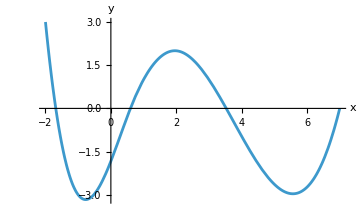

```mathematica
plot11G = Plot[f11[x],{x,minx,maxx}]
```

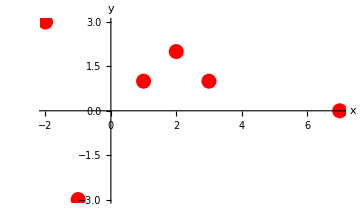

```mathematica
plot11P=ListPlot[data11,PlotStyle->{PointSize[0.03],Red}]
```

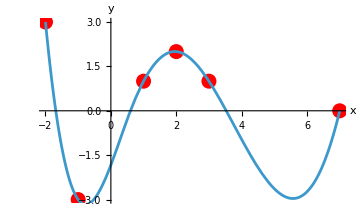

```mathematica
Show[plot11P,plot11G]
```

```mathematica
(* Problem 2 *)
```

```mathematica
x12=Transpose[data11][[1]]
```

{1,-2,-1,7,3,2}

```mathematica
y12=Transpose[data11][[2]]
```

{1,3,-3,0,1,2}

```mathematica
sx12:=Interpolation[x12,Method->"Spline"]
```

```mathematica
sy12:=Interpolation[y12,Method->"Spline"]
```

```mathematica
spline12[t_]:={sx12[t],sy12[t]}
```

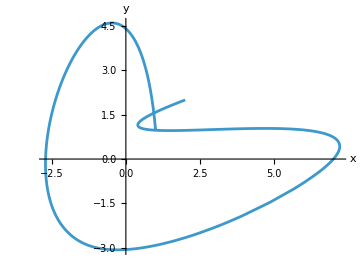

```mathematica
plot12=ParametricPlot[spline12[t],{t,1,Length[x12]}]
```

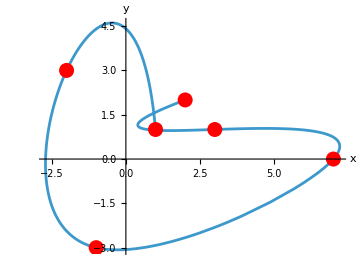

```mathematica
Show[plot12,plot11P]
```

```mathematica
(* Problem 3 *)
```

```mathematica
data3={{-3,-1},{-1,-2},{1,-2},{2,-3},{1,-4},{-1,-4},{-2,-5},{-2,-6},{-1,-6},{-1,-5},{2,-5},{3,-4},{6,-5},{7,-7},{6,-8},{6,-9},{7,-9},{7,-8},{8,-7},{7,-4},{6,-4},{6,-2},{5,0},{10,-1},{7,0},{10,0},{7,1},{10,2},{8,2},{10,3},{6,2},{5,0},{3,0},{1,2},{1,3},{-2,6},{-3,6},{-4,7},{-4,6},{-6,4},{-6,3},{-5,3},{-3,4},{-2,2},{-3,1},{-5,2},{-7,0},{-7,-1},{-6,-1},{-6,0},{-5,1},{-4,0},{-5,-2},{-3,-4},{-2,-4},{-2,-3},{-3,-3},{-4,-2},{-3,-1}};
```

```mathematica
horsex=Transpose[data3][[1]]
```

{-3,-1,1,2,1,-1,-2,-2,-1,-1,2,3,6,7,6,6,7,7,8,7,6,6,5,10,7,10,7,10,8,10,6,5,3,1,1,-2,-3,-4,-4,-6,-6,-5,-3,-2,-3,-5,-7,-7,-6,-6,-5,-4,-5,-3,-2,-2,-3,-4,-3}

```mathematica
horsey=Transpose[data3][[2]]
```

{-1,-2,-2,-3,-4,-4,-5,-6,-6,-5,-5,-4,-5,-7,-8,-9,-9,-8,-7,-4,-4,-2,0,-1,0,0,1,2,2,3,2,0,0,2,3,6,6,7,6,4,3,3,4,2,1,2,0,-1,-1,0,1,0,-2,-4,-4,-3,-3,-2,-1}

```mathematica
interhx:=Interpolation[horsex,Method->"Spline"]
```

```mathematica
interhy:=Interpolation[horsey,Method->"Spline"]
```

```mathematica
horseSpline[t_]:={interhx[t],interhy[t]}
```

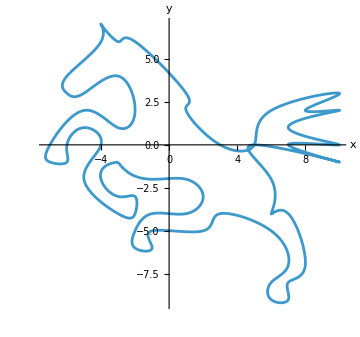

```mathematica
plot12=ParametricPlot[horseSpline[t],{t,1,Length[horsex]}]
```

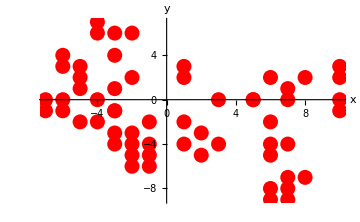

```mathematica
Plot32=ListPlot[data3,PlotStyle->{PointSize[0.03],Red}]
```

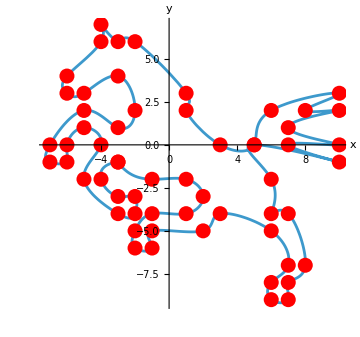

```mathematica
Show[{plot12,Plot32}]
```

```mathematica
Plane3=ParametricPlot3D[{u,5,v},{u,-10,10},{v,-10,10},BoxRatios->1,PlotStyle->Black]
```

-Graphics3D-

```mathematica
horse3DD[t_]:={interhx[t],5,interhy[t]}
```

```mathematica
Horse3=ParametricPlot3D[horse3DD[t],{t,0,Length[horsex]},PlotStyle->Green]
```

-Graphics3D-

```mathematica
VerticalHorse=Show[Horse3,Plane3]
```

-Graphics3D-

```mathematica
(* Problem 4 *)
```

```mathematica
data14={{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,4},{5,3,2},{7,5,6},{5,5,5}}
```

{{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,4},{5,3,2},{7,5,6},{5,5,5}}

```mathematica
plot14P=ListPointPlot3D[data14,PlotStyle->PointSize[0.05]]
```

-Graphics3D-

```mathematica
x14 = Transpose[data14][[1]]
```

{1,2,1,4,4,5,7,5}

```mathematica
y14 = Transpose[data14][[2]]
```

{1,3,3,3,4,3,5,5}

```mathematica
z14 = Transpose[data14][[3]]
```

{1,1,2,3,4,2,6,5}

```mathematica
sx14=Interpolation[x14]
```

InterpolatingFunction[…]

```mathematica
sy14=Interpolation[y14]
```

InterpolatingFunction[…]

```mathematica
sz14=Interpolation[z14]
```

InterpolatingFunction[…]

```mathematica
s14[t_]:={sx14[t],sy14[t],sz14[t]}
```

```mathematica
LinePlotHaha=ParametricPlot3D[s14[t],{t,1,Length[x14]},PlotStyle->Orange]
```

-Graphics3D-

```mathematica
Show[{LinePlotHaha, plot14P}]
```

-Graphics3D-

```mathematica
(* Problem 5 *)
```

```mathematica
plot5:=ParametricPlot3D[s14[t],{t,1,Length[x14]},PlotStyle->{clr5,Thickness[th5]}]
```

```mathematica
plot5P=ListPointPlot3D[data14,PlotStyle->{PointSize[0.05],Magenta}]
```

-Graphics3D-

```mathematica
plot5All:=Show[{plot5,plot5P}]
```

```mathematica
MyMenu5:=PopupMenu[Dynamic[clr5],{Red->"Red",Green->"Green",Blue->"Blue",Purple->"Purple"}]
```

```mathematica
MySlider5:=Slider[Dynamic[th5],{0,0.025,0.001}]
```

```mathematica
{Dynamic[plot5All],MyMenu5,MySlider5}
```

{,,}

```mathematica
(* Bonus *)
```